```mathematica
SetDirectory[NotebookDirectory[]];
```

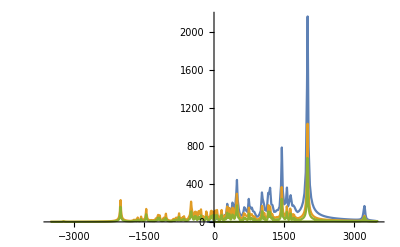

```mathematica
numMode=200;sd55=ArrayReshape[#,{numMode,2}]&@BinaryReadList["./bj_55.dat","Real32"];sd300=ArrayReshape[#,{800,2}]&@BinaryReadList["./bj_300.dat","Real32"];jl=ArrayReshape[#,{800,2}]&@BinaryReadList["./jl.dat","Real32"];ListLinePlot[{sd55,sd300,jl},PlotRange->{{-3500,3500},All}]
```

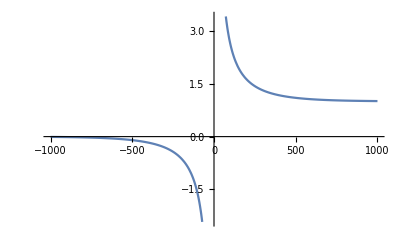

```mathematica
temp[t_,w_]:=0.5(1+Coth[(w/2)/(0.69503 t)]);Plot[temp[300,w],{w,-1000,1000}]
```